# Cálculos Iniciais em LT aérea

## Antonio Carlos Siqueira de Lima 2022/1

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\anton\Dropbox\UFRJ\cursos\EEE457-Transmissão_Energia_Elétrica\arquivos_Mma_EEE457

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=80.0 ; (* comprimento do circuito *)
```

```mathematica
z=0.12160464662817234 + 0.48366929205670867 I;
y= 3.447800169070513*^-6 ⅈ;
Zc= Sqrt[z/y];
θ= Sqrt[ z y]ℓ;
```

## Definição do quadripolo

```mathematica
Q={{Cosh[θ],Zc Sinh[θ]},{1/Zc Sinh[θ], Cosh[θ]}};
MatrixForm[Q]
```

(0.994668+0.00133927 ⅈ | 9.69379+38.6291 ⅈ
-1.23222×10^-7+0.000275334 ⅈ | 0.994668+0.00133927 ⅈ)

```mathematica
Det[Q]
```

1.+0. ⅈ

```mathematica
Vr = 138. 10^3/Sqrt[3]
```

79674.3

## Carregamento puramente resistivo

```mathematica
P= 50. 10^6;
Ir= 50. 10^6/(Sqrt[3] 138 10^3)
```

209.185

```mathematica
y ℓ/2 Vr
```

0.+10.988 ⅈ

```mathematica
{Vs, Is}=Q.{Vr, Ir}
```

{81277.3+8187.33 ⅈ,208.06+22.2172 ⅈ}

```mathematica
vs= Vs Sqrt[3]/138000.;
ib= 50 10^6/(Sqrt[3] 138000.);
```

```mathematica
is= Is/ib;
```

```mathematica
Abs[vs]
```

1.02528

```mathematica
Abs[is]
```

1.00028

```mathematica
Arg[vs]/π 180
```

5.75219

```mathematica
Arg[Is]/π 180
```

6.0951

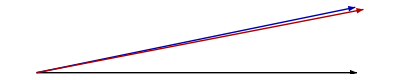

```mathematica
Graphics[{Arrow[{{0,0}, {1,0}}],{Darker@Blue, Arrow[{{0,0},{ Re[is], Im[is]}}]}, {Darker@ Red, Arrow[{{0,0}, {Re[vs], Im[vs]}}]}}]
```

## Carregamento indutivo (0,95 fp)

```mathematica
Si= P/0.95;
```

```mathematica
Iri=Si/(Sqrt[3] 138 10^3)Exp[-I ArcCos[0.95]];
```

```mathematica
Arg[Iri]/π 180
```

-18.1949

```mathematica
{Vsi, Isi}=Q.{Vr, Iri};
```

```mathematica
vsi= Vsi Sqrt[3]/138000.;
ibi= 50/0.95 10^6/(Sqrt[3] 138000.);
isi= Isi/ibi;
iri= Iri/ibi;
```

```mathematica
Abs[vsi]
```

1.05768

```mathematica
iri
```

0.95-0.31225 ⅈ

```mathematica
Abs[isi]
```

0.968285

```mathematica
Arg[vsi]/π 180
```

5.1203

```mathematica
Arg[Isi]/π 180
```

-12.5068

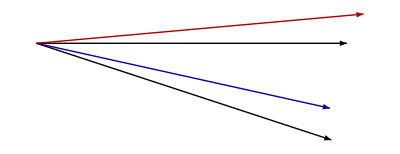

```mathematica
Graphics[{Arrow[{{0,0}, {1,0}}],Arrow[{{0,0},{Re[iri], Im[iri]}}]
,{Darker@Blue, Arrow[{{0,0},{ Re[isi], Im[isi]}}]}, {Darker@ Red, Arrow[{{0,0}, {Re[vsi], Im[vsi]}}]}}]
```

```mathematica
Re[vsi Conjugate[isi]]-Re[1 Conjugate[iri]]
```

0.026046

## Carregamento capacitivo (0,95 fp)

```mathematica
Sc= P/0.95;
```

```mathematica
Irc=Si/(Sqrt[3] 138 10^3)Exp[I ArcCos[0.95]];
```

```mathematica
Arg[Irc]/π 180
```

18.1949

```mathematica
{Vsc, Isc}=Q.{Vr, Irc};
```

```mathematica
vsc= Vsc Sqrt[3]/138000.;
ibc= 50/0.95 10^6/(Sqrt[3] 138000.);
isc= Isc/ibc;
irc= Irc/ibc;
```

```mathematica
Abs[vsc]
```

0.993021

```mathematica
irc
```

0.95+0.31225 ⅈ

```mathematica
Abs[isc]
```

1.03022

```mathematica
Arg[vsc]/π 180
```

6.42521

```mathematica
Arg[Isc]/π 180
```

23.5416

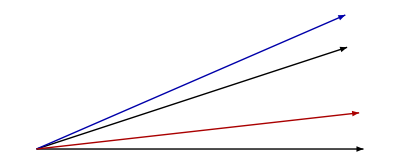

```mathematica
Graphics[{Arrow[{{0,0}, {1,0}}],Arrow[{{0,0},{Re[irc], Im[irc]}}]
,{Darker@Blue, Arrow[{{0,0},{ Re[isc], Im[isc]}}]}, {Darker@ Red, Arrow[{{0,0}, {Re[vsc], Im[vsc]}}]}}]
```

```mathematica
Re[vsc Conjugate[isc]]-Re[1 Conjugate[irc]]
```

0.0277158